## Rabi

```mathematica
path="/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/parameter_scans_20190221";
dataSets=Import[#,"CSV"]⟦All,2;;⟧&/@(FileNames[FileNameJoin@{FileNameJoin@{path,"rabi_constantfun_scan"},"*"}]);
Dimensions@dataSets

joinedDataSets=Join@@(Rest/@dataSets);
Dimensions@joinedDataSets
```

{57,201,3}

{11400,3}

```mathematica
ListPlot3D[joinedDataSets,InterpolationOrder->3,AxesLabel->{"time","height","fidelity"}]
```

-Graphics3D-

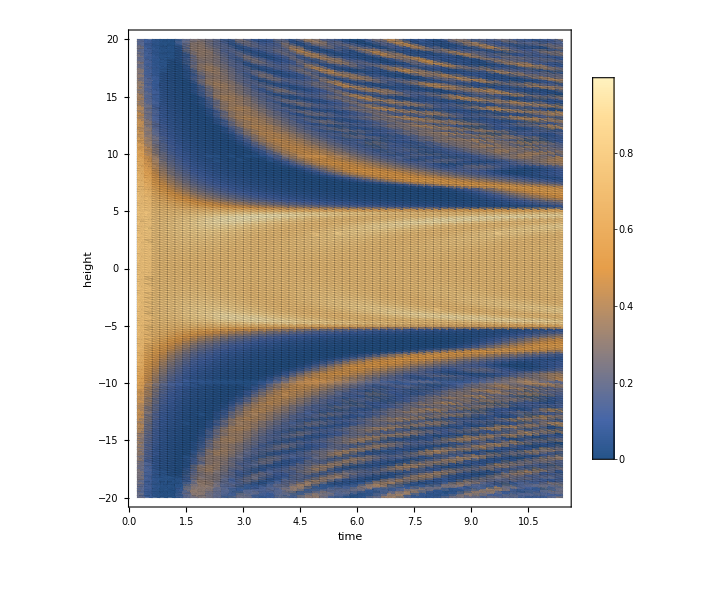

```mathematica
ListDensityPlot[joinedDataSets,PlotLegends->Automatic,Mesh->All,MeshStyle->Directive[Opacity@0.1],FrameLabel->{"time","height"},ImageSize->600]
```

## Rabi finer search

```mathematica
path="/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/parameter_scans_20190221";
dataSets=Import[#,"CSV"]⟦All,2;;⟧&/@(FileNames[FileNameJoin@{FileNameJoin@{path,"rabi_constantfun_scan_finerSearch"},"*"}]);
Dimensions@dataSets

joinedDataSets=Join@@(Rest/@dataSets);
Dimensions@joinedDataSets
```

{68,201,3}

{13600,3}

```mathematica
ListPlot3D[joinedDataSets,InterpolationOrder->3,AxesLabel->{"time","height","fidelity"},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
ListDensityPlot[joinedDataSets,PlotLegends->Automatic,Mesh->All,MeshStyle->Directive[Opacity@0.1],FrameLabel->{"time","height"},ImageSize->600]
```

-Graphics-

## LMG

```mathematica
<<MaTeX`
dataSets=Import[#,"CSV"]⟦All,2;;⟧&/@(FileNames[FileNameJoin@{FileNameJoin@{NotebookDirectory[],"lmg_constantfun_scan"},"*"}]);
Dimensions@dataSets

joinedDataSets=Join@@(Rest/@dataSets);
Dimensions@joinedDataSets
```

{80,201,3}

{16000,3}

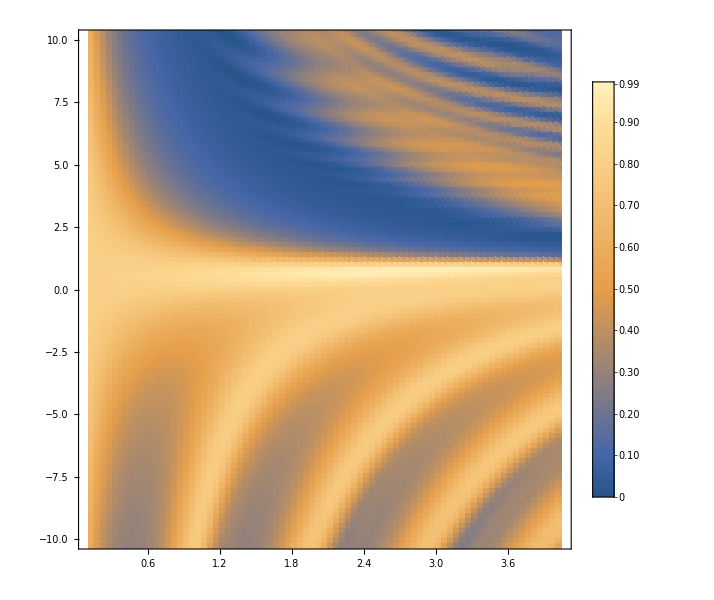

```mathematica
fig=ListDensityPlot[joinedDataSets,
FrameLabel->{MaTeX["\\omega\\tau",Magnification->2.2],MaTeX["g_{\\rm max}",Magnification->2.2]},ImageSize->600,
Mesh->None,MeshStyle->Directive[Opacity@0.1],PlotRangePadding->None,
LabelStyle->Directive[Black,FontFamily->"DejaVu Sans",FontSize->20],
PlotLegends->BarLegend[Automatic, Ticks->N@Append[Subdivide[0,1,10],0.99],LegendMarkerSize->540,LegendMargins->0],
PlotRange->{All,{-10,10}}
(*Epilog->{Point@maxPoints⟦All,;;2⟧}*)
]
```

Extract heights for which we get maximum fidelity

```mathematica
MinMax@joinedDataSets⟦All,-1⟧
```

{0.000046282,0.995718}

```mathematica
Export["lmg_constprotscan_t0-4_heightpm10.png",fig,ImageResolution->200]
```

lmg_constprotscan_t0-4_heightpm10.png

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"lmg_constprotscan_t0-4_heightpm10.png"},fig,ImageResolution->500]
```

/home/lk/Documents/docs/research/Ricardo/quantum-control-critical-point/results/parameter_scans_20190221/lmg_constprotscan_t0-4_heightpm10.png

```mathematica
SystemOpen@NotebookDirectory[]
```

```mathematica
pivotedList=Table[Select[joinedDataSets,#⟦1⟧==t&],
{t,joinedDataSets⟦All,1⟧//DeleteDuplicates}];
```

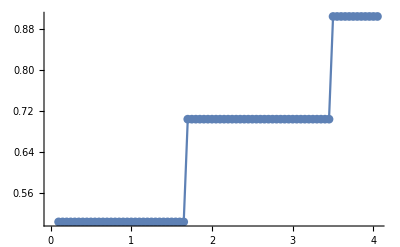

```mathematica
maxPoints=Map[Last@SortBy[Last]@#&,#,{1}]&@GatherBy[joinedDataSets,First];
ListPlot[maxPoints⟦All,;;2⟧,Joined->True,PlotMarkers->Automatic]
```

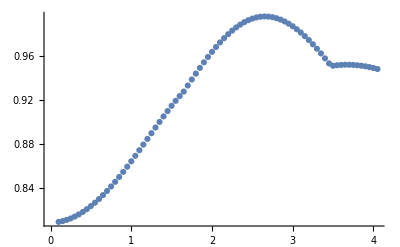

```mathematica
ListPlot[maxPoints⟦All,{1,3}⟧]
```

Does using log10 infidelity scale work better? (meh)

```mathematica
fig=ListDensityPlot[{#⟦1⟧,#⟦2⟧,Log10[1-#⟦3⟧]}&/@joinedDataSets,
FrameLabel->{MaTeX["\\Delta\\tau",Magnification->2.2],MaTeX["\\mathcal F",Magnification->2.2]},ImageSize->600,
Mesh->None,MeshStyle->Directive[Opacity@0.1],PlotRangePadding->None,
LabelStyle->Directive[Black,FontFamily->"DejaVu Sans",FontSize->20],
PlotLegends->Automatic
]
```

```mathematica
ListPlot3D[joinedDataSets,
AxesLabel->{"time","height","fidelity"},PlotRange->{All,All,All},InterpolationOrder->1,
ColorFunction->"TemperatureMap",PlotLegends->Automatic,ImageSize->600
]
```

-Graphics3D-

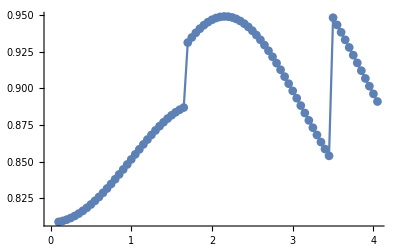

```mathematica
bestFidelityPerTime=Function[dataset,
First@dataset⟦Ordering[#,-1,#1⟦3⟧<#2⟦3⟧&]&[dataset⟦2;;,All⟧]⟧
]/@dataSets;
ListPlot[bestFidelityPerTime⟦All,{1,3}⟧,Joined->True,PlotMarkers->Automatic]
```